```mathematica
(* =====================================================================
   0. Setup — 载入数据
   ===================================================================== *)
dataDir = "D:\\tsmcN40_lookup";
scriptDir = FileNameJoin[{dataDir, "mathematica"}];
Get[FileNameJoin[{scriptDir, "tsmcN40_lookup.wl"}]];

nch[corner_] := LoadTsmcN40[FileNameJoin[{dataDir, "nch_" <> corner <> ".h5"}]];
pch[corner_] := LoadTsmcN40[FileNameJoin[{dataDir, "pch_" <> corner <> ".h5"}]];

tt = nch["tt"];
corners = {"tt", "ff", "ss", "fs", "sf"};

(* --- 数据网格信息 --- *)
vars4 = Select[Keys[tt], (ArrayQ[tt[#]] && Length[Dimensions[tt[#]]] == 4) &];
Style[Grid[{
   {"器件", tt["DEVICE"] <> " " <> tt["CORNER"], "W=" <> ToString[tt["W"]] <> " um, T=" <> ToString[tt["TEMP"]] <> " K"},
   {"VSB", ToString[Length[tt["VSB"]]] <> " 点", tt["VSB"]},
   {"VDS", ToString[Length[tt["VDS"]]] <> " 点",
    ToString[Min[tt["VDS"]]] <> " .. " <> ToString[Max[tt["VDS"]]] <> " V, 步长 " <>
     ToString[tt["VDS"][[2]] - tt["VDS"][[1]]]},
   {"VGS", ToString[Length[tt["VGS"]]] <> " 点",
    ToString[Min[tt["VGS"]]] <> " .. " <> ToString[Max[tt["VGS"]]] <> " V, 步长 " <>
     ToString[tt["VGS"][[2]] - tt["VGS"][[1]]]},
   {"L", ToString[Length[tt["L"]]] <> " 点", tt["L"]}},
  Dividers -> All, Spacings -> {1.5, 0.6}, Background -> {None, LightGray},
  ItemStyle -> {Bold, Bold}],
 FontFamily -> "Microsoft YaHei"]

Ls = {0.04, 0.1, 0.18, 0.35, 1.0};
cols = ColorData["Rainbow"][#] & /@ Subdivide[0, 0.9, Length[Ls] - 1];
vgs = tt["VGS"];

(* 固定 (VSB,VDS) 沿 VGS 扫出各 L 的一组曲线 *)
fam[data_, var_, vsb_, vds_, Ls_] :=
  With[{fi = N40Interpolant[data, var]},
    Table[Map[fi[L, #, vds, vsb] &, vgs], {L, Ls}]];

legend[Ls_] := LineLegend[cols, Map["L=" <> ToString[#] <> " um" &, Ls],
  LegendLabel -> "L"];
```

器件 | nch tt | W=10 um, T=300 K
VSB | 9 点 | {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8}
VDS | 56 点 | 0. .. 1.1 V, 步长 0.02
VGS | 56 点 | 0. .. 1.1 V, 步长 0.02
L | 48 点 | {0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.2,1.4,1.6,1.8,2.,2.5,3.,4.,5.}

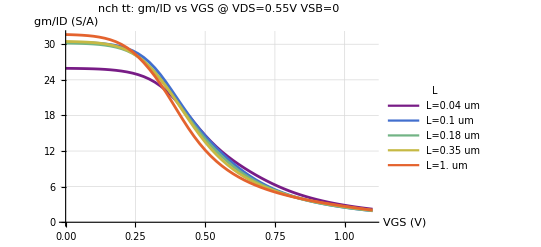

```mathematica
(* =====================================================================
   1. gm/ID vs VGS  — 弱反型峰值应 ≈ 25~35，强反型单调下降、无毛刺
   ===================================================================== *)
ListLinePlot[fam[tt, "GM_ID", 0, 0.55, Ls], DataRange -> {0, 1.1},
 PlotStyle -> cols, PlotLegends -> legend[Ls],
 AxesLabel -> {"VGS (V)", "gm/ID (S/A)"},
 PlotLabel -> "nch tt: gm/ID vs VGS  @ VDS=0.55V VSB=0",
 GridLines -> Automatic]
```

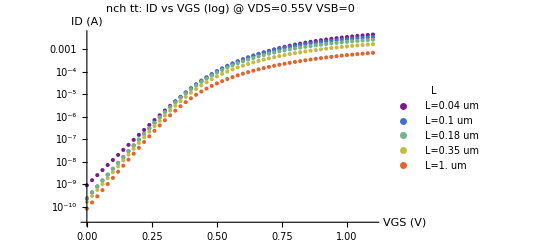

```mathematica
(* =====================================================================
   2. ID vs VGS（对数） — 亚阈区应呈直线、无折点/双峰；VGS=0 为关断电流
   ===================================================================== *)
ListLogPlot[fam[tt, "ID", 0, 0.55, Ls], DataRange -> {0, 1.1},
 PlotStyle -> cols, PlotLegends -> legend[Ls],
 AxesLabel -> {"VGS (V)", "ID (A)"},
 PlotLabel -> "nch tt: ID vs VGS (log)  @ VDS=0.55V VSB=0",
 GridLines -> Automatic]
```

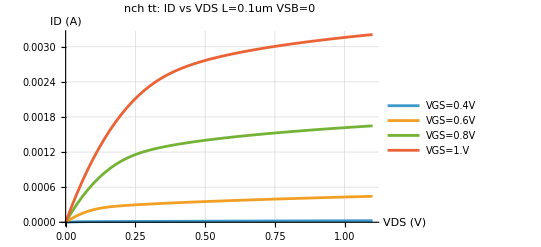

```mathematica
(* =====================================================================
   3. ID vs VDS（输出特性族） — 饱和区应平坦、无扭结(kink)、无异常反弹
   ===================================================================== *)
vgsO = {0.4, 0.6, 0.8, 1.0};
With[{fi = N40Interpolant[tt, "ID"], vd = tt["VDS"]},
  ListLinePlot[
    Table[{vds, fi[0.1, vg, vds, 0]}, {vg, vgsO}, {vds, vd}],
    AxesLabel -> {"VDS (V)", "ID (A)"},
    PlotLabel -> "nch tt: ID vs VDS  L=0.1um VSB=0",
    PlotLegends -> LineLegend[Automatic, Map["VGS=" <> ToString[#] <> "V" &, vgsO]],
    GridLines -> Automatic]]
```

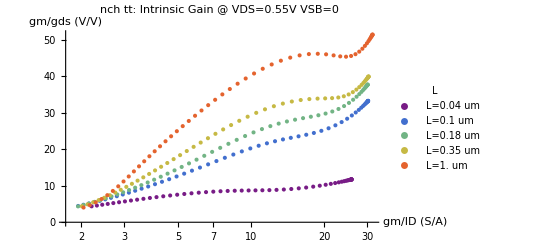

```mathematica
(* =====================================================================
   4. 本征增益 GAIN = gm/gds vs gm/ID
   ===================================================================== *)
ListLogLinearPlot[
  Transpose[#] & /@ Transpose[{fam[tt, "GM_ID", 0, 0.55, Ls],
     fam[tt, "GAIN", 0, 0.55, Ls]}],
  PlotStyle -> cols, PlotLegends -> legend[Ls],
  AxesLabel -> {"gm/ID (S/A)", "gm/gds (V/V)"},
  PlotLabel -> "nch tt: Intrinsic Gain  @ VDS=0.55V VSB=0",
  GridLines -> Automatic]
```

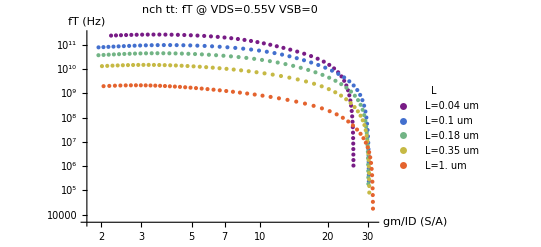

```mathematica
(* =====================================================================
   5. fT vs gm/ID
   ===================================================================== *)
ListLogLogPlot[
  Transpose[#] & /@ Transpose[{fam[tt, "GM_ID", 0, 0.55, Ls],
     fam[tt, "FT", 0, 0.55, Ls]}],
  PlotStyle -> cols, PlotLegends -> legend[Ls],
  AxesLabel -> {"gm/ID (S/A)", "fT (Hz)"},
  PlotLabel -> "nch tt: fT  @ VDS=0.55V VSB=0",
  GridLines -> Automatic]
```

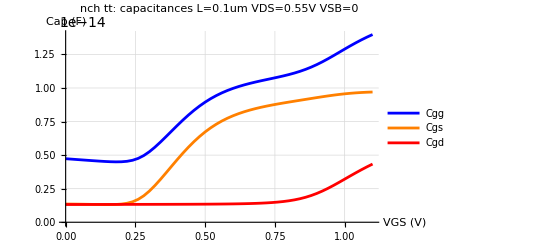

```mathematica
(* =====================================================================
   6. 电容 Cgg / Cgs / Cgd vs VGS  — 应>0 且平滑、量级合理
   ===================================================================== *)
With[{fg = N40Interpolant[tt, "CGG"], fs = N40Interpolant[tt, "CGS"],
   fd = N40Interpolant[tt, "CGD"]},
  ListLinePlot[{
    Map[fg[0.1, #, 0.55, 0] &, vgs],
    Map[fs[0.1, #, 0.55, 0] &, vgs],
    Map[fd[0.1, #, 0.55, 0] &, vgs]},
   DataRange -> {0, 1.1}, PlotRange -> All,
   PlotStyle -> {Blue, Orange, Red},
   PlotLegends -> LineLegend[{"Cgg", "Cgs", "Cgd"}],
   AxesLabel -> {"VGS (V)", "Cap (F)"},
   PlotLabel -> "nch tt: capacitances  L=0.1um VDS=0.55V VSB=0",
   GridLines -> Automatic]]
```

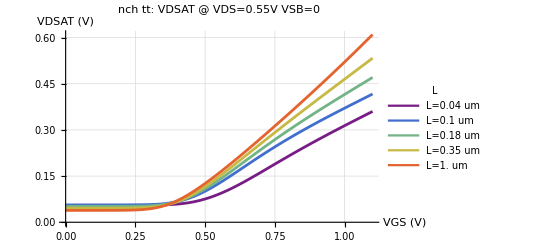

```mathematica
(* =====================================================================
   7. VDSAT vs VGS  — 强反型 VDSAT ≈ 2/(gm/ID)
   ===================================================================== *)
ListLinePlot[fam[tt, "VDSAT", 0, 0.55, Ls], DataRange -> {0, 1.1},
 PlotStyle -> cols, PlotLegends -> legend[Ls],
 AxesLabel -> {"VGS (V)", "VDSAT (V)"},
 PlotLabel -> "nch tt: VDSAT  @ VDS=0.55V VSB=0",
 GridLines -> Automatic]
```

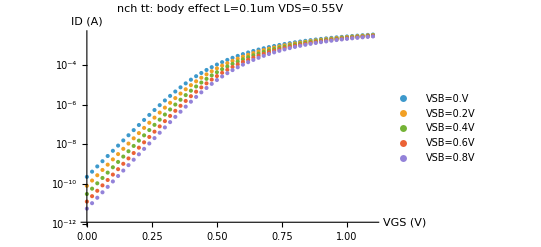

```mathematica
(* =====================================================================
   8. 体效应 — ID vs VGS, VSB=0..0.8 （VT 应随 |VSB| 增大、亚阈斜率略变）
   ===================================================================== *)
With[{fi = N40Interpolant[tt, "ID"], vsbs = {0.0, 0.2, 0.4, 0.6, 0.8}},
  ListLogPlot[
    Table[Map[fi[0.1, #, 0.55, vsb] &, vgs], {vsb, vsbs}],
    DataRange -> {0, 1.1}, PlotStyle -> Automatic,
    PlotLegends -> LineLegend[Automatic, Map["VSB=" <> ToString[#] <> "V" &, vsbs]],
    AxesLabel -> {"VGS (V)", "ID (A)"},
    PlotLabel -> "nch tt: body effect  L=0.1um VDS=0.55V",
    GridLines -> Automatic]]
```

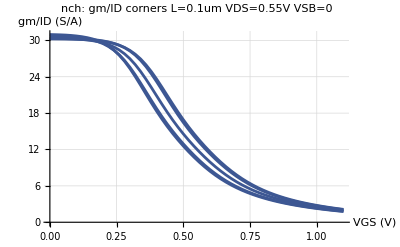

```mathematica
(* =====================================================================
   9. 工艺角对比 — 固定偏置下 gm/ID 与 ID 随 corner 的散布
   (注意: 构造待值形式得用 With 先绑定，否则会对每个 VGS 点重复加载/重建插值)
   ===================================================================== *)
ListLinePlot[
  Table[
    With[{fi = N40Interpolant[nch[c], "GM_ID"]},
      Map[fi[0.1, #, 0.55, 0] &, vgs]],
    {c, corners}],
  DataRange -> {0, 1.1},
  PlotStyle -> ColorData["DarkRainbow"][#] & /@ Subdivide[0, 1, Length[corners] - 1],
  PlotLegends -> LineLegend[Automatic, corners],
  AxesLabel -> {"VGS (V)", "gm/ID (S/A)"},
  PlotLabel -> "nch: gm/ID corners  L=0.1um VDS=0.55V VSB=0",
  GridLines -> Automatic]
```

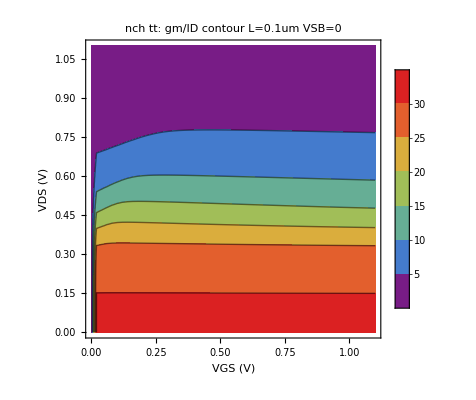

```mathematica
(* =====================================================================
   10. gm/ID 二维云图 (VGS, VDS) — 检查网格覆盖/连续性
   ===================================================================== *)
With[{f = N40Interpolant[tt, "GM_ID"]},
  ListContourPlot[
    Flatten[Table[{vds, vgs, f[0.1, vgs, vds, 0]},
      {vds, 0, 1.1, 0.02}, {vgs, 0, 1.1, 0.02}], 1],
   FrameLabel -> {"VGS (V)", "VDS (V)"},
   PlotLabel -> "nch tt: gm/ID contour  L=0.1um VSB=0",
   ColorFunction -> "Rainbow", PlotLegends -> Automatic]]
```

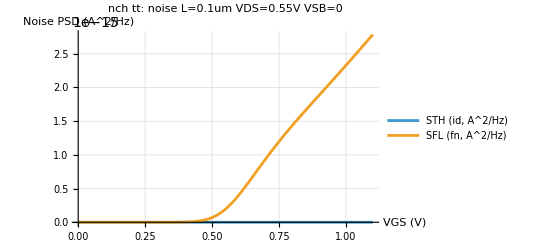

```mathematica
(* =====================================================================
   11. 噪声 STH / SFL vs VGS — 关断区为 NaN(空)、开启区应有合理量级
   ===================================================================== *)
With[{fs = N40Interpolant[tt, "STH"], fl = N40Interpolant[tt, "SFL"]},
  ListLinePlot[{
    Map[fs[0.1, #, 0.55, 0] &, vgs],
    Map[fl[0.1, #, 0.55, 0] &, vgs]},
   DataRange -> {0, 1.1}, PlotRange -> All,
   PlotLegends -> LineLegend[{"STH (id, A^2/Hz)", "SFL (fn, A^2/Hz)"}],
   AxesLabel -> {"VGS (V)", "Noise PSD (A^2/Hz)"},
   PlotLabel -> "nch tt: noise  L=0.1um VDS=0.55V VSB=0",
   GridLines -> Automatic]]
```

```mathematica
(* =====================================================================
   12. 数据质量报告
   ===================================================================== *)
nanFrac[arr_] := N[Total[Flatten@Boole[Map[! NumericQ[#] &, arr, {-1}]]] /
    Max[1, Length[Flatten[arr]]]];
idarr = tt["ID"];
neg = Flatten@Table[Select[Differences[idarr[[il, All, id, iv]]], # < 0 &],
    {il, 48}, {id, 56}, {iv, 9}];
off = Max[Flatten@Table[idarr[[il, 1, id, iv]], {il, 48}, {id, 56}, {iv, 9}]];
Style[Grid[{
   {"变量", "NaN/非数值占比"},
   {"STH", nanFrac[tt["STH"]]}, {"SFL", nanFrac[tt["SFL"]]},
   {"ID", nanFrac[tt["ID"]]}, {"GM", nanFrac[tt["GM"]]},
   {"FT", nanFrac[tt["FT"]]}, {"GAIN", nanFrac[tt["GAIN"]]},
   {"CGG", nanFrac[tt["CGG"]]}},
  Dividers -> All, Spacings -> {2, 0.5}, Background -> {None, LightGray},
  ItemStyle -> {Bold, Bold}, Alignment -> Left],
 FontFamily -> "Microsoft YaHei"]
Style[Grid[{
   {"ID 沿 VGS 单调性（负增量个数）",
    ToString[Length[neg]]},
   {"ID 沿 VGS 单调性（最大负增量）",
    ToString[If[Length[neg] > 0, Min[neg], 0.]]},
   {"最大关断电流 ID@VGS=0 (A)",
    ScientificForm[off, 6]}},
  Dividers -> All, Spacings -> {2, 0.5}, Background -> {None, Automatic},
  ItemStyle -> {Bold, Bold}, Alignment -> Left],
 FontFamily -> "Microsoft YaHei"]
```

变量 | NaN/非数值占比
STH | 0.
SFL | 0.
ID | 0.
GM | 0.
FT | 0.
GAIN | 0.
CGG | 0.

ID 沿 VGS 单调性（负增量个数） | 0
ID 沿 VGS 单调性（最大负增量） | 0.
最大关断电流 ID@VGS=0 (A) | 2.54171×10^-9